{0.0004649,0.0006237,0.0031684,0.0107633}

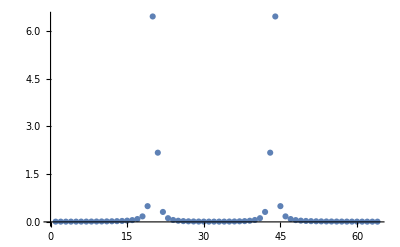

```mathematica
exn[n_]:=Table[
Exp[I s k/n 2 Pi],
{k,1,n},{s,1,n}]
ω=2;
n=8;
dftTime={};
Do[
fs=Table[0.1 Sin[ω arg],{arg,1,n}];
(*простое дискретное преобразование*)
(*k -строка; s- столбец*)
(*Матрица коэффициентов для ДПФ*)
res =AbsoluteTiming[
ex=Table[
Exp[I s k/n 2 Pi],
{k,1,n},{s,1,n}];
g=ex.fs;];
AppendTo[dftTime,res[[1]]];
n=2 n;
,{i,1,4}]
dftTime
(*Это амплитуды. Точные решения - функции дирака. Вообще, они ещё симметричны относительно 0*)
ListPlot[Abs[g]^2,PlotRange->All]
```

```mathematica
FFT[arr_,n_]:=
Module[{f1,f2,g1,g2,n2,gi,gii,tmp},
f1=arr[[1;;-1;;2]] ;(*нечетные*)
f2=arr[[2;;-1;;2]];  (*четные*)
n2=n/2;
If[n2==4,
tmp=exn[n2];
gi=tmp.f1;
gii=tmp.f2
,(*else*)
gi=FFT[f1,n2];
gii=FFT[f2,n2];
];

g1=Table[Exp[-I k/n 2 Pi] gi[[k]],{k,1,n2}]+gii;
g2=Table[Exp[-I k/n 2 Pi] gi[[k-n2]],{k,n2+1,n}]+gii;
Join[g1,g2]
];
```

```mathematica
mass={0,8,0,5,2,0,0,1,1,4,0,6,2,0,0,0};

Length[mass]
FFT[mass,Length[mass]]-exn[Length[mass]].mass //Simplify
```

16

{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}

```mathematica
(*
Посчёт сложности (по операциям/времени): T(n)=2T(n/2)+O(n)=4T(n/4)+O(n)=...=O(log(n)n)
T(n)<= const*n+ 2T(n/2)<=const*n + const* 2 n/2 + 4T(n/4)<=...<=const*n Σ k(1); k =log_2(n)
*)

ω=4;
n=8;
fftTime={};
Do[
fs=Table[0.1 Sin[ω arg],{arg,1,n}];
(*простое дискретное преобразование*)
(*k -строка; s- столбец*)
(*Матрица коэффициентов для ДПФ*)
res =AbsoluteTiming[
FFT[fs,n]
];
AppendTo[fftTime,res[[1]]];
n=2 n;

,{i,1,13}]
fftTime
```

{0.0652816,0.0002339,0.0004392,0.0038878,0.0026076,0.0055117,0.0142535,0.0313198,0.063621,0.14262,0.305612,0.721501,1.54951}

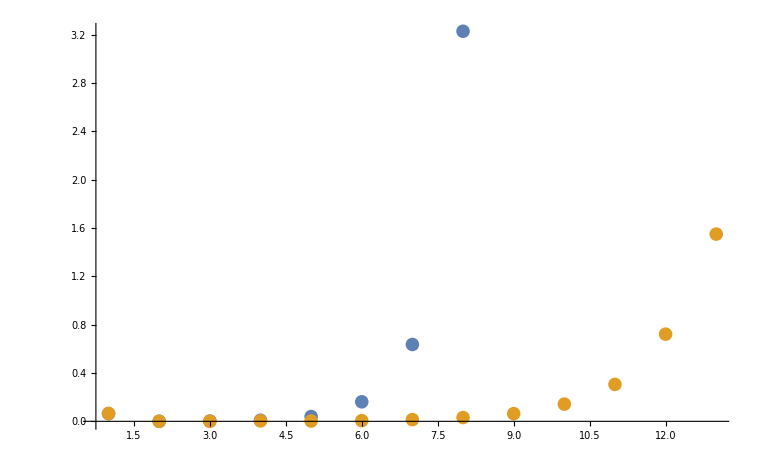

```mathematica
ListPlot[{
dftTime, fftTime},PlotRange->All] (*На оси Х величина не существенной*)
```

```mathematica
(* 
Когда ДПФ плохо работает?
Теорема Котельникова-Шенона. О том что непрерывный сигнал можно представить в виде интерполяционного ряда, когда интервал дискретизации δ<=1/2ω (или частота дикретизации >2ω), где ω - частота исходного сигнала.
--
Использовать частоту дискретизации,по крайней мере вдвое превышающую максимальную частоту присутствующую в исходном сигнале. (Иногда можно сделать без этого, но с костылями.)
*)
```